```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with e^ik bc *)
hk[k_,n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->Exp[I k]tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
ρ=.5;
n=16;
{val,vec}=Eigensystem[hk[0,n,ρ,1.]];
o=Ordering[val];
val=val[[o]];
vec=vec[[o]];
wf=Transpose[vec];
G0[ω_,i_]:=Total[Abs[wf[[i]]]^2/(val-ω)];
```

```mathematica
G0[-1.5,1]
```

0.153696

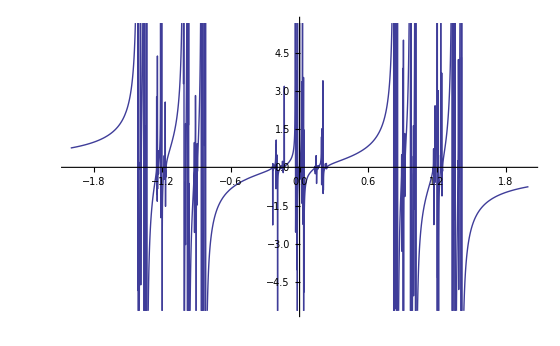

```mathematica
Plot[G0[ω,1],{ω,-2,2}]
```

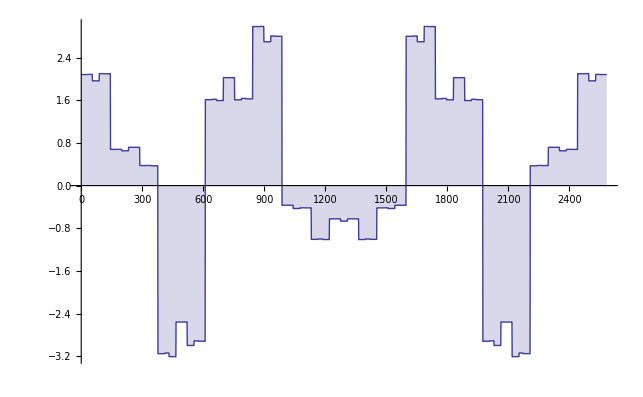

```mathematica
DiscretePlot[G0[1.3,i],{i,Fibonacci[n+2]}]
```

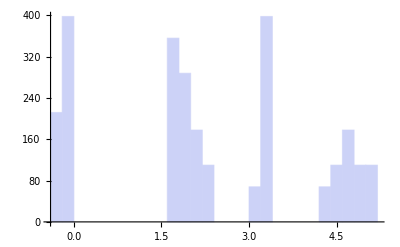

```mathematica
dat=Table[G0[0.8,i],{i,Fibonacci[n+2]}];
Histogram[dat,20,PlotRange->All]
```